# Compute a kernel mixture of the crime data from NYC

## import the data

### import the data on crime in 2014 and 2015

```mathematica
data2014=SemanticImport[FileNameJoin[{NotebookDirectory[],"2014.csv"}]];
```

```mathematica
data2015=SemanticImport[FileNameJoin[{NotebookDirectory[],"2015.csv"}]];
```

```mathematica
data20142015=Join[data2014,data2015];
```

We’ll just use 2014 data for now.

### kernel estimation

Some of our data is erroneously in PA:

```mathematica
data2014[1;;5000,{"latitude","longitude"}/*Values/*GeoPosition][GeoListPlot]
```

-Graphics-

Let’s only consider data points whose position is within 20 miles of NYC:

```mathematica
GeoPosition[LinguisticAssistant]
```

GeoPosition[{40.6643,-73.9385}]

```mathematica
GeoListPlot[{GeoPosition[{40.6642738,-73.9385004}]}]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[GeoPosition[LinguisticAssistant],Quantity[20,"Miles"]]]
```

-Graphics-

```mathematica
dataWithin20MilesOfNYC=data2014[Select[GeoDistance[GeoPosition[{40.6642738,-73.9385004}],GeoPosition[{#latitude,#longitude}]]<Quantity[20,"Miles"]&]]
```

That removed 21 data points:

```mathematica
Length@%
```

25979

## Smoothing the crime data

#### choosing a bandwidth

```mathematica
Module[{bw=0.1},Plot3D[Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],bw],{x,y}],{x,smallBox⟦1,1,1⟧,smallBox⟦2,1,1⟧},{y,smallBox⟦1,1,2⟧,smallBox⟦2,1,2⟧},PlotLabel->Row[{"bandwidth = ",N@bw}],ImageSize->Medium,PlotRange->Full,Filling->Axis,PlotLabel->"bandwidth = "<>ToString[bw]]]
```

-Graphics3D-

```mathematica
Module[{bw=0.0005},Plot3D[Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],bw],{x,y}],{x,smallBox⟦1,1,1⟧,smallBox⟦2,1,1⟧},{y,smallBox⟦1,1,2⟧,smallBox⟦2,1,2⟧},PlotLabel->Row[{"bandwidth = ",N@bw}],ImageSize->Medium,PlotRange->Full,Filling->Axis,PlotLabel->"bandwidth = "<>ToString[bw]]]
```

-Graphics3D-

```mathematica
Module[{bw=0.001},Plot3D[Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],bw],{x,y}],{x,smallBox⟦1,1,1⟧,smallBox⟦2,1,1⟧},{y,smallBox⟦1,1,2⟧,smallBox⟦2,1,2⟧},PlotLabel->Row[{"bandwidth = ",N@bw}],ImageSize->Medium,PlotRange->Full,Filling->Axis,PlotLabel->"bandwidth = "<>ToString[bw]]]
```

-Graphics3D-

```mathematica
Module[{bw=0.0003},Plot3D[Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],bw],{x,y}],{x,smallBox⟦1,1,1⟧,smallBox⟦2,1,1⟧},{y,smallBox⟦1,1,2⟧,smallBox⟦2,1,2⟧},PlotLabel->Row[{"bandwidth = ",N@bw}],ImageSize->Medium,PlotRange->Full,Filling->Axis,PlotLabel->"bandwidth = "<>ToString[bw]]]
```

-Graphics3D-

```mathematica
Export["bandwidth_0p0003.pdf",%413];
```

### the final choice of bandwidth

The characteristic scale is h=33 meters:

```mathematica
0.0003*111320
```

33.396

```mathematica
Module[{bw=0.0003},Plot3D[Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],bw],{x,y}],{x,smallBox⟦1,1,1⟧,smallBox⟦2,1,1⟧},{y,smallBox⟦1,1,2⟧,smallBox⟦2,1,2⟧},PlotLabel->Row[{"bandwidth = ",N@bw}],ImageSize->Medium,PlotRange->Full,Filling->Axis,PlotLabel->"bandwidth = "<>ToString[bw]]]
```

-Graphics3D-

## Compute the risk of each edge in midtown

```mathematica
kmd0p0003Func[{lat_,long_}]:=Evaluate@PDF[KernelMixtureDistribution[Normal[dataWithin20MilesOfNYC[All,{"latitude","longitude"}/*Values]],0.0003],{lat,long}];
```

```mathematica
dataWithRisk=ParallelMap[Join[#,<|"risk"->kmd0p0003Func[#["alat"],#["along"]]+kmd0p0003Func[(#["alat"]+#["blat"])/2.,(#["along"]+#["blong"])/2.]+kmd0p0003Func[#["blat"],#["blong"]]|>]&,Normal[routingPairsDS[All]]];//Timing
```

{82.13355,Null}

```mathematica
Dataset[dataWithRisk]
```

### import routing pairs

```mathematica
columnHeadings={"aID","bID","alat","along","blat","blong"};
```

```mathematica
routingPairsDS=Dataset[Association[Thread[columnHeadings->#]]&/@Take[routingPairs,All]];
```

### export it

```mathematica
Export["dataWithRisk2.txt",Normal@Values@dataWithRisk⟦1;;-1⟧]
```

dataWithRisk2.txt

### histogram of risk values

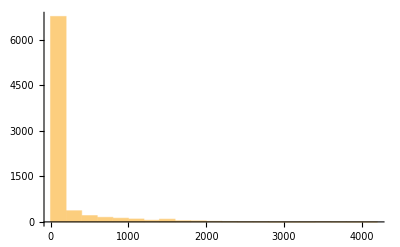

```mathematica
Dataset[dataWithRisk][All,"risk"][Histogram]
```

```mathematica
Dataset[dataWithRisk][Max,"risk"]
```

4144.76